```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Estimator Parameters: Length of Wilson Lines:*)
L:=10
(*Number of Time Steps:*)
n:=10
(*Distance between instanton and anti-instanton*)
R:=1
(*Distance between quark and anti-quark*)
r:=1
(*Integration Bounds*)
l:=3
```

```mathematica
η:=Array[Eta,{4,4,3}]
Do[Eta[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Eta[4,4,a]=0,{a,1,3}]
Do[Eta[k,4,a]=KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Eta[4,k,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
ηbar:=Array[Etabar,{4,4,3}]
Do[Etabar[k,l,a]=LeviCivitaTensor[3][[k,l,a]]
,{k,1,3},{l,1,3},{a,1,3}]
Do[Etabar[4,4,a]=0,{a,1,3}]
Do[Etabar[k,4,a]=-KroneckerDelta[k,a],{k,1,3},{a,1,3}]
Do[Etabar[4,k,a]=+KroneckerDelta[k,a],{k,1,3},{a,1,3}]
```

```mathematica
(*Test Values*)
ypoint={1.,1.,0.,0.};
```

```mathematica
(*Instanton rotation*)
Rvec:=
R{0,0,0,1}
```

```mathematica
(*Ratio Ansatz*)
Ya[y_]:=y+Rvec/2
Yi[y_]:=y-Rvec/2
Arot[y_]:=
Table[
Sum[(-η[[mu]][[nu]][[a]]*2*Ya[y][[nu]]/(Ya[y].Ya[y])^2-
ηbar[[mu]][[nu]][[a]]*2*Yi[y][[nu]]/(Yi[y].Yi[y])^2),{nu,1,4}]/(1+1/(Ya[y].Ya[y])+1/(Yi[y].Yi[y]))
,{mu,1,4},{a,1,3}](*Table[Sum[(ηbar[[μ,ν,aa]]*Yi[y][[ν]]*Ya[y].Ya[y]+η[[μ,ν,aa]]*Ya[y][[ν]]*Yi[y].Yi[y])/((Yi[y].Yi[y])(Ya[y].Ya[y])+Yi[y].Yi[y]+Ya[y].Ya[y]),{ν,1,4}],{μ,1,4},{aa,1,3}]*)
Dimensions[Arot[ypoint]]
```

{4,3}

```mathematica
(*Wilson Line at a point in time*)
W2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]/2]+I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]/2]
Wd2[a_]:=IdentityMatrix[2]*Cos[L/n*Sqrt[a[[4]].a[[4]]]/2]-I*(Sum[a[[4]][[i]]/Sqrt[a[[4]].a[[4]]]PauliMatrix[i],{i,1,3}])Sin[L/n*Sqrt[a[[4]].a[[4]]]/2]
```

```mathematica
(*Table of wilson lines along L*)
WList[y_,rot_]:=Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,n}]
WdList[y_,rot_]:=Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,n}]
```

```mathematica
(*Matrix Product*)
Wapprox[y_,rot_]:=Dot@@WList[y,rot] (* applies the function to everything in the table *)
Wdapprox[y_,rot_]:=Dot@@WdList[y,rot]
```

```mathematica
(*Upper and Lower Lines for B fields*)
WApproxUpper[y_,rot_,t_]:=Dot@@Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,t+1,n}]
WApproxLower[y_,rot_,t_]:=Dot@@Table[W2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,t}]
WdApproxUpper[y_,rot_,t_]:=Dot@@Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,t+1,n}]
WdApproxLower[y_,rot_,t_]:=Dot@@Table[Wd2[Arot[y+rot.{0,0,0,(i-1/2)L/n-L/2}]],{i,1,t}]
```

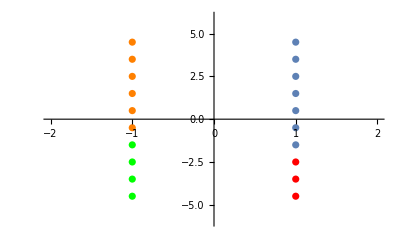

```mathematica
t1=3;
t2=4;
contour1=ListPlot[Table[{1,(i-1/2)L/n-L/2},{i,t1+1,n}],PlotRange->{{-2,2},{-6,6}}];
contour2=ListPlot[Table[{1,(i-1/2)L/n-L/2},{i,1,t1}],PlotStyle->Red];
contour3=ListPlot[Table[{-1,(i-1/2)L/n-L/2},{i,t2+1,n}],PlotRange->{-6,6},PlotStyle->Orange];
contour4=ListPlot[Table[{-1,(i-1/2)L/n-L/2},{i,1,t2}],PlotStyle->Green];
Show[contour1,contour2,contour3,contour4]
```

```mathematica
WapproxHoriz[y_,rot_,rr_]:=Dot@@Table[W2[Arot[rot.y+rot.{(i-1/2)rr/n-rr/2,0,0,L/2}]],{i,1,n}]
```

```mathematica
Horiz[y_,rot_,rr_]:=Sqrt[1-(1/2Tr[WapproxHoriz[y,rot,rr]])^2]
```

```mathematica
FindMaximum[Horiz[{y,0,0,0},IdentityMatrix[4],2],{y,-2.5}]
FindMaximum[Horiz[{y,0,0,0},{{Cos[θ],0,0,Sin[θ]},
{0,1,0,0},
{0,0,1,0},
{-Sin[θ],0,0,Cos[θ]}},2],{{y,-2.5},{θ,0}}]
```

{0.0151588,{y→-2.35261}}

{0.0284373,{y→-0.00257269,θ→-0.767326}}

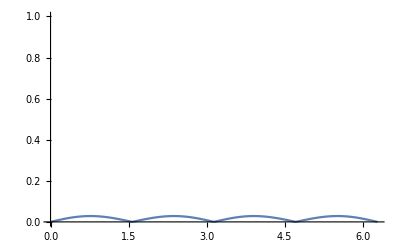

```mathematica
Plot[Horiz[{0.002,0,0,0},{{Cos[θ],0,0,Sin[θ]},
{0,1,0,0},
{0,0,1,0},
{-Sin[θ],0,0,Cos[θ]}},2],{θ,0,2Pi},PlotRange->{0,1}]
```

```mathematica
(*WapproxHoriz[{-3.64,0,0,0},{{Cos[1.74],0,0,Sin[1.74]},
{0,1,0,0},
{0,0,1,0},
{-Sin[1.74],0,0,Cos[1.74]}},2]*)
```

```mathematica
Imes[y_,rot_,rr_]:=Re[1-1/2*Tr[Wapprox[y+rot.{rr/2,0,0,0},rot].Wdapprox[y-rot.{rr/2,0,0,0},rot]]](* integrand *)
```

```mathematica
(*Obtaining random spherically distributed points.*)
RandSphere:=Module[{r,poi},r=2;
While[r>1,
poi=RandomReal[{-1,1},4];
r=Norm[poi]]; 
poi=poi/r;
poi ]
{RandSphere,RandSphere}
(*ListPlot[Table[randSphere,100],AspectRatio->1]*)
```

{{-0.581391,0.556799,0.593206,0.00817624},{0.4406,0.522492,0.52378,0.508457}}

```mathematica
(*Random sampling of rotation matricies*)
RotR[a_]:=
{{a[[1]],-a[[2]],-a[[3]],-a[[4]]},
{a[[2]],a[[1]],-a[[4]],a[[3]]},
{a[[3]],a[[4]],a[[1]],-a[[2]]},
{a[[4]],-a[[3]],a[[2]],a[[1]]}};
RotL[p_]:={{p[[1]],-p[[2]],-p[[4]],-p[[3]]},
{p[[2]],p[[1]],p[[3]],-p[[4]]},
{p[[4]],-p[[3]],p[[1]],p[[2]]},
{p[[3]],p[[4]],-p[[2]],p[[1]]}};
Rot[a_,p_]:=RotL[a].RotR[p]
RandRot:=Rot[RandSphere,RandSphere]
```

```mathematica
RandY:=Append[RandomReal[{-l,l},3],0]
```

```mathematica
(*0.05-0.1 for rotating the lines*)
(*Similar range for rotating the fields*)
Timing[Imes[RandY,RandRot,5]]
```

{0.03125,0.0042652}

```mathematica
(*Number of test points for monte carlo*)
num=100;
l=3;
```

```mathematica
(*Random numbers for all future points*)
(*randRot=Table[RandRot,11,num];
randY=Table[randRot[[i,j]].RandY,{i,1,11},{j,1,num}];
randRot2=Table[RandRot,11,num];
randY2=Table[randRot[[i,j]].RandY,{i,1,11},{j,1,num}];*)
```

```mathematica
(*Unit conversion to GeV and multiplication by instanton density 12/2*)
units=43.7;
(*Conversion from ρ to GeV^-1*)
unitsr=1.4;
(*Step size in r*)
rstep=0.8;
```

```mathematica
DistanceDataMesList=Table[Module[{rot, y},rot=RandRot;
y=rot.RandY;
units*8l^3/num*Imes[y,rot,rr/unitsr]],{rr,0,8,0.8},{i,1,num}];
```

```mathematica
data1=Table[{rr,Around[8l^3/num*Sum[DistanceDataMesList[[rr/rstep+1,i]],{i,1,num}],8l^3/Sqrt[num]*Variance[DistanceDataMesList[[rr/rstep+1]]]]},{rr,0,10rstep,rstep}]
```

{{0.,39.35.},{0.8,103.182.},{1.6,186.250.},{2.4,321.503.},{3.2,213.220.},{4.,345.512.},{4.8,285.266.},{5.6,111.29.},{6.4,128.106.},{7.2,107.54.},{8.,0.31.110^3}}

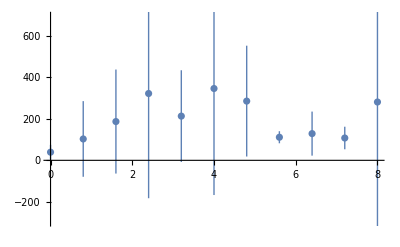

```mathematica
PlotMesMC=ListPlot[Re[data1]]
```

```mathematica
(*Field Strength*)
Fmunu=Table[D[Arot[{y[1],y[2],y[3],y[4]}][[mu]][[a]],y[nu] ]-D[Arot[{y[1],y[2],y[3],y[4]}][[nu]][[a]],y[mu] ],{mu,1,4},{nu,1,4},{a,1,3}]+Table[
-Sum[
LeviCivitaTensor[3][[a,b,c]]Arot[{y[1],y[2],y[3],0}][[mu]][[b]]Arot[{y[1],y[2],y[3],0}][[nu]][[c]],{b,1,3},{c,1,3}],
{mu,1,4},{nu,1,4},{a,1,3}];
Dimensions[Fmunu]
```

{4,4,3}

```mathematica
B[yy_]:=Table[1/2Sum[LeviCivitaTensor[3][[i]][[j]][[k]](Fmunu[[j,k,a]]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]})PauliMatrix[a] ,{j,1,3},{k,1,3},{a,1,3}],{i,1,3}]
Ee[yy_]:=Table[1/2Sum[(Fmunu[[4,i,a]]/.{y[1]->yy[[1]],y[2]->yy[[2]],y[3]->yy[[3]],y[4]->yy[[4]]})PauliMatrix[a] ,{a,1,3}],{i,1,3}]
```

```mathematica
B[RandY][[1]]
Ee[RandY][[1]]
```

{{-0.0249223,0.0319006-0.00218103 ⅈ},{0.0319006+0.00218103 ⅈ,0.0249223}}

{{0.,0.+0. ⅈ},{0.+0. ⅈ,0.}}

```mathematica
(*Integrand for two B fields*)
ImesBB[y_,rot_,rr_,t1_,t2_]:=Sum[Tr[WApproxLower[y+rot.{rr/2,0,0,0},rot,t1].B[y+rot.{rr/2,0,0,0}+rot.{0,0,0,t1}][[i]].WApproxUpper[y+rot.{rr/2,0,0,0},rot,t1].WdApproxUpper[y-rot.{rr/2,0,0,0},rot,t2].B[y-rot.{rr/2,0,0,0}+rot.{0,0,0,t2}][[i]].WdApproxLower[y-rot.{rr/2,0,0,0},rot,t2]],{i,1,3}]
```

```mathematica
AbsoluteTiming[Sum[ImesBB[RandY,RandRot,3,t1,t2](L/n)^2,{t1,1,n},{t2,1,n}]]
```

$Aborted

```mathematica
num=100;
randRot=Table[RandRot,11,num];
randY=Table[randRot[[i,j]].RandY,{i,1,11},{j,1,num}];
```

```mathematica
DistanceDataMesBB[rY_,rR_]:=Table[{rr,units*8l^3/num*Sum[Sum[ImesBB[rY[[rr/0.5+1,i]],rR[[rr/0.5+1,i]],rr/unitsr,t1,t2](L/n)^2,{t1,1,n},{t2,1,n}],{i,1,num}]},{rr,0,5,0.5}]
```

```mathematica
data1BB=DistanceDataMesBB[randY,randRot]
```

{{0.,27301.7+0. ⅈ},{0.5,8054.15+0. ⅈ},{1.,1376.66+0. ⅈ},{1.5,1504.33+0. ⅈ},{2.,462.679+0. ⅈ},{2.5,140.77+0. ⅈ},{3.,439.736+0. ⅈ},{3.5,-7.15806+0. ⅈ},{4.,153.611+0. ⅈ},{4.5,-200.154+0. ⅈ},{5.,-65.2629+0. ⅈ}}

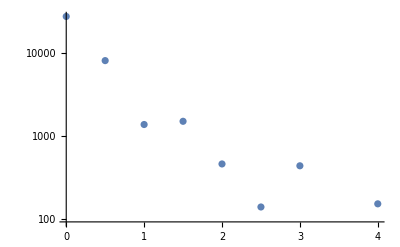

```mathematica
ListLogPlot[data1BB]
```

```mathematica
(*SU(3) matrix for baryon*)
Wapprox3[y_,rot_]:=SparseArray[ArrayFlatten[{{Wapprox[y,rot],0},{0,1}}]]
```

```mathematica
(*SU(2) Structure*)
Cc[y_,rot_]:=1/2Tr[Wapprox[y,rot]]
Ss[y_,rot_]:=Sqrt[1-Cc[y,rot]^2]
Nhat[y_,rot_]:=Table[1/(2)Tr[PauliMatrix[i].Wapprox[y,rot]]/(I*Ss[y,rot]),{i,1,3}]
Nhat[randY[[1,1]],randRot[[1,1]]]
Nhat[randY[[1,1]],randRot[[1,1]]].Nhat[randY[[1,1]],randRot[[1,1]]]
```

{-0.113968+0. ⅈ,0.979354+0. ⅈ,0.166962+0. ⅈ}

1.+0. ⅈ

```mathematica
IbarStruc=1/3 (C1 C2+C1 C3+C2 C3+S1 S2 n1hat⟦3⟧ n2hat⟦3⟧+S2 S3 n2hat⟦1⟧ n3hat⟦1⟧+S1 n1hat⟦1⟧ (S2 n2hat⟦1⟧+S3 n3hat⟦1⟧)+S2 S3 n2hat⟦2⟧ n3hat⟦2⟧+S1 n1hat⟦2⟧ (S2 n2hat⟦2⟧+S3 n3hat⟦2⟧)+S1 S3 n1hat⟦3⟧ n3hat⟦3⟧+S2 S3 n2hat⟦3⟧ n3hat⟦3⟧);
```

Part::partd: Part specification n1hat⟦3⟧ is longer than depth of object.

Part::partd: Part specification n2hat⟦3⟧ is longer than depth of object.

Part::partd: Part specification n2hat⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Baryon Integrand-Direct Triangle*)
Ibar[y_,rot_,rr_]:=1-IbarStruc/.{C1->Cc[y+rot.{1/Sqrt[3]*rr,0,0,0},rot],S1->Ss[y+rot.{1/Sqrt[3]*rr,0,0,0},rot],n1hat->Nhat[y+rot.{1/Sqrt[3]*rr,0,0,0},rot],C2->Cc[y+rot.{-1/(2Sqrt[3])*rr,1/(2)*rr,0,0},rot],S2->Ss[y+rot.{-1/(2Sqrt[3])*rr,1/(2)*rr,0,0},rot],n2hat->Nhat[y+rot.{-1/(2Sqrt[3])*rr,1/(2)*rr,0,0},rot],
C3->Cc[y+rot.{-1/(2Sqrt[3])*rr,-1/(2)*rr,0,0},rot],S3->Ss[y+rot.{-1/(2Sqrt[3])*rr,-1/(2)*rr,0,0},rot],n3hat->Nhat[y+rot.{-1/(2Sqrt[3])*rr,-1/(2)*rr,0,0},rot]}
```

```mathematica
Timing[Ibar[RandY,RandRot,2]]
```

{0.390625,0.000798179+0. ⅈ}

```mathematica
num=1000;
l=3;
randRot=Table[RandRot,11,num];
randY=Table[randRot[[i,j]].RandY,{i,1,11},{j,1,num}];
```

```mathematica
DistanceDataBar=Table[Module[{rot, y},rot=RandRot;
y=rot.RandY;
units*8l^3/num*Ibar[y,rot,rr/unitsr]],{rr,0,8,0.8},{i,1,num}];
```

{{0.,5.88954×10^-13+0. ⅈ},{0.8,222.476+0. ⅈ},{1.6,416.001+0. ⅈ},{2.4,568.181+0. ⅈ},{3.2,567.313+0. ⅈ},{4.,547.665+0. ⅈ},{4.8,523.28+0. ⅈ},{5.6,520.77+0. ⅈ},{6.4,397.876+0. ⅈ},{7.2,431.696+0. ⅈ},{8.,269.749+0. ⅈ}}

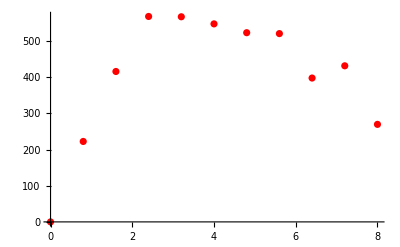

```mathematica
PlotBar=ListPlot[DistanceDataBar,PlotStyle->Red]
```

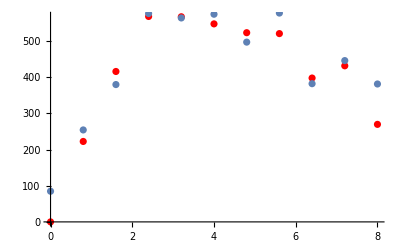

```mathematica
Show[PlotBar, PlotMesMC]
```

```mathematica
Wdapprox3[y_,rot_]:=SparseArray[ArrayFlatten[{{Wapprox[y,rot],0},{0,1}}]]
```

```mathematica
TetraStructure[wd1_,wd2_,wd3_,wd4_]=Permute[{wd1,wd2,wd3,wd4},SymmetricGroup[4]]
```

{{wd1,wd2,wd3,wd4},{wd1,wd2,wd4,wd3},{wd1,wd3,wd2,wd4},{wd1,wd3,wd4,wd2},{wd1,wd4,wd2,wd3},{wd1,wd4,wd3,wd2},{wd2,wd1,wd3,wd4},{wd2,wd1,wd4,wd3},{wd2,wd3,wd1,wd4},{wd2,wd3,wd4,wd1},{wd2,wd4,wd1,wd3},{wd2,wd4,wd3,wd1},{wd3,wd1,wd2,wd4},{wd3,wd1,wd4,wd2},{wd3,wd2,wd1,wd4},{wd3,wd2,wd4,wd1},{wd3,wd4,wd1,wd2},{wd3,wd4,wd2,wd1},{wd4,wd1,wd2,wd3},{wd4,wd1,wd3,wd2},{wd4,wd2,wd1,wd3},{wd4,wd2,wd3,wd1},{wd4,wd3,wd1,wd2},{wd4,wd3,wd2,wd1}}

```mathematica
1-1/(24*3^4)*Sum[Tr[Wapprox3[y,rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,1]]]Tr[Wapprox3[y+{rr,0,0,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,2]]]Tr[Wapprox3[y+{0,rr,0,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,3]]]Tr[Wapprox3[y+{0,0,rr,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,4]]],{i,1,24}]
```

```mathematica
(*Looking at W's sturcturally*)
Wstruc[c_,s_,nhat_]:=c*IdentityMatrix[2]+Sum[nhat[[i]]PauliMatrix[i],{i,1,3}]s
Wdstruc[c_,s_,nhat_]:=c*IdentityMatrix[2]-Sum[nhat[[i]]PauliMatrix[i],{i,1,3}]s
```

```mathematica
Wdvars={Wdstruc[c1,s1,n1hat],Wdstruc[c2,s2,n2hat],Wdstruc[c3,s3,n3hat],Wdstruc[c4,s4,n4hat]};
```

Part::partd: Part specification n1hat⟦1⟧ is longer than depth of object.

Part::partd: Part specification n1hat⟦2⟧ is longer than depth of object.

Part::partd: Part specification n1hat⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(TetraStructure@@(Wdvars[RandY,RandRot,5]))[[1,1]]
```

SparseArray[…]

```mathematica
ItetraStruc=Simplify[Sum[Tr[Wdstruc[c1,s1,n1hat].(TetraStructure@@Wdvars)[[i,1]]]Tr[Wdstruc[c2,s2,n2hat].(TetraStructure@@Wdvars)[[i,2]]]Tr[Wdstruc[c3,s3,n3hat].(TetraStructure@@Wdvars)[[i,3]]]Tr[Wdstruc[c4,s4,n4hat].(TetraStructure@@Wdvars)[[i,4]]],{i,1,24}]]
```

Part::partd: Part specification n1hat⟦1⟧ is longer than depth of object.

Part::partd: Part specification n1hat⟦2⟧ is longer than depth of object.

Part::partd: Part specification n1hat⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

16 ((c2 c3+s2 s3 n2hat⟦1⟧ n3hat⟦1⟧+s2 s3 n2hat⟦2⟧ n3hat⟦2⟧+s2 s3 n2hat⟦3⟧ n3hat⟦3⟧)^2 (c1 c4+s1 s4 n1hat⟦1⟧ n4hat⟦1⟧+s1 s4 n1hat⟦2⟧ n4hat⟦2⟧+s1 s4 n1hat⟦3⟧ n4hat⟦3⟧)^2+(c2^2+s2^2 n2hat⟦1⟧^2+s2^2 n2hat⟦2⟧^2+s2^2 n2hat⟦3⟧^2) (c3^2+s3^2 n3hat⟦1⟧^2+s3^2 n3hat⟦2⟧^2+s3^2 n3hat⟦3⟧^2) (c1 c4+s1 s4 n1hat⟦1⟧ n4hat⟦1⟧+s1 s4 n1hat⟦2⟧ n4hat⟦2⟧+s1 s4 n1hat⟦3⟧ n4hat⟦3⟧)^2+2 (c1 c3+s1 s3 n1hat⟦1⟧ n3hat⟦1⟧+s1 s3 n1hat⟦2⟧ n3hat⟦2⟧+s1 s3 n1hat⟦3⟧ n3hat⟦3⟧) (c2 c3+s2 s3 n2hat⟦1⟧ n3hat⟦1⟧+s2 s3 n2hat⟦2⟧ n3hat⟦2⟧+s2 s3 n2hat⟦3⟧ n3hat⟦3⟧) (c1 c4+s1 s4 n1hat⟦1⟧ n4hat⟦1⟧+s1 s4 n1hat⟦2⟧ n4hat⟦2⟧+s1 s4 n1hat⟦3⟧ n4hat⟦3⟧) (c2 c4+s2 s4 n2hat⟦1⟧ n4hat⟦1⟧+s2 s4 n2hat⟦2⟧ n4hat⟦2⟧+s2 s4 n2hat⟦3⟧ n4hat⟦3⟧)+2 (c1 c2+s1 s2 n1hat⟦1⟧ n2hat⟦1⟧+s1 s2 n1hat⟦2⟧ n2hat⟦2⟧+s1 s2 n1hat⟦3⟧ n2hat⟦3⟧) (c3^2+s3^2 n3hat⟦1⟧^2+s3^2 n3hat⟦2⟧^2+s3^2 n3hat⟦3⟧^2) (c1 c4+s1 s4 n1hat⟦1⟧ n4hat⟦1⟧+s1 s4 n1hat⟦2⟧ n4hat⟦2⟧+s1 s4 n1hat⟦3⟧ n4hat⟦3⟧) (c2 c4+s2 s4 n2hat⟦1⟧ n4hat⟦1⟧+s2 s4 n2hat⟦2⟧ n4hat⟦2⟧+s2 s4 n2hat⟦3⟧ n4hat⟦3⟧)+(c1 c3+s1 s3 n1hat⟦1⟧ n3hat⟦1⟧+s1 s3 n1hat⟦2⟧ n3hat⟦2⟧+s1 s3 n1hat⟦3⟧ n3hat⟦3⟧)^2 (c2 c4+s2 s4 n2hat⟦1⟧ n4hat⟦1⟧+s2 s4 n2hat⟦2⟧ n4hat⟦2⟧+s2 s4 n2hat⟦3⟧ n4hat⟦3⟧)^2+(c1^2+s1^2 n1hat⟦1⟧^2+s1^2 n1hat⟦2⟧^2+s1^2 n1hat⟦3⟧^2) (c3^2+s3^2 n3hat⟦1⟧^2+s3^2 n3hat⟦2⟧^2+s3^2 n3hat⟦3⟧^2) (c2 c4+s2 s4 n2hat⟦1⟧ n4hat⟦1⟧+s2 s4 n2hat⟦2⟧ n4hat⟦2⟧+s2 s4 n2hat⟦3⟧ n4hat⟦3⟧)^2+2 (c2^2+s2^2 n2hat⟦1⟧^2+s2^2 n2hat⟦2⟧^2+s2^2 n2hat⟦3⟧^2) (c1 c3+s1 s3 n1hat⟦1⟧ n3hat⟦1⟧+s1 s3 n1hat⟦2⟧ n3hat⟦2⟧+s1 s3 n1hat⟦3⟧ n3hat⟦3⟧) (c1 c4+s1 s4 n1hat⟦1⟧ n4hat⟦1⟧+s1 s4 n1hat⟦2⟧ n4hat⟦2⟧+s1 s4 n1hat⟦3⟧ n4hat⟦3⟧) (c3 c4+s3 s4 n3hat⟦1⟧ n4hat⟦1⟧+s3 s4 n3hat⟦2⟧ n4hat⟦2⟧+s3 s4 n3hat⟦3⟧ n4hat⟦3⟧)+2 (c1 c2+s1 s2 n1hat⟦1⟧ n2hat⟦1⟧+s1 s2 n1hat⟦2⟧ n2hat⟦2⟧+s1 s2 n1hat⟦3⟧ n2hat⟦3⟧) (c2 c3+s2 s3 n2hat⟦1⟧ n3hat⟦1⟧+s2 s3 n2hat⟦2⟧ n3hat⟦2⟧+s2 s3 n2hat⟦3⟧ n3hat⟦3⟧) (c1 c4+s1 s4 n1hat⟦1⟧ n4hat⟦1⟧+s1 s4 n1hat⟦2⟧ n4hat⟦2⟧+s1 s4 n1hat⟦3⟧ n4hat⟦3⟧) (c3 c4+s3 s4 n3hat⟦1⟧ n4hat⟦1⟧+s3 s4 n3hat⟦2⟧ n4hat⟦2⟧+s3 s4 n3hat⟦3⟧ n4hat⟦3⟧)+2 (c1 c2+s1 s2 n1hat⟦1⟧ n2hat⟦1⟧+s1 s2 n1hat⟦2⟧ n2hat⟦2⟧+s1 s2 n1hat⟦3⟧ n2hat⟦3⟧) (c1 c3+s1 s3 n1hat⟦1⟧ n3hat⟦1⟧+s1 s3 n1hat⟦2⟧ n3hat⟦2⟧+s1 s3 n1hat⟦3⟧ n3hat⟦3⟧) (c2 c4+s2 s4 n2hat⟦1⟧ n4hat⟦1⟧+s2 s4 n2hat⟦2⟧ n4hat⟦2⟧+s2 s4 n2hat⟦3⟧ n4hat⟦3⟧) (c3 c4+s3 s4 n3hat⟦1⟧ n4hat⟦1⟧+s3 s4 n3hat⟦2⟧ n4hat⟦2⟧+s3 s4 n3hat⟦3⟧ n4hat⟦3⟧)+2 (c1^2+s1^2 n1hat⟦1⟧^2+s1^2 n1hat⟦2⟧^2+s1^2 n1hat⟦3⟧^2) (c2 c3+s2 s3 n2hat⟦1⟧ n3hat⟦1⟧+s2 s3 n2hat⟦2⟧ n3hat⟦2⟧+s2 s3 n2hat⟦3⟧ n3hat⟦3⟧) (c2 c4+s2 s4 n2hat⟦1⟧ n4hat⟦1⟧+s2 s4 n2hat⟦2⟧ n4hat⟦2⟧+s2 s4 n2hat⟦3⟧ n4hat⟦3⟧) (c3 c4+s3 s4 n3hat⟦1⟧ n4hat⟦1⟧+s3 s4 n3hat⟦2⟧ n4hat⟦2⟧+s3 s4 n3hat⟦3⟧ n4hat⟦3⟧)+(c1 c2+s1 s2 n1hat⟦1⟧ n2hat⟦1⟧+s1 s2 n1hat⟦2⟧ n2hat⟦2⟧+s1 s2 n1hat⟦3⟧ n2hat⟦3⟧)^2 (c3 c4+s3 s4 n3hat⟦1⟧ n4hat⟦1⟧+s3 s4 n3hat⟦2⟧ n4hat⟦2⟧+s3 s4 n3hat⟦3⟧ n4hat⟦3⟧)^2+(c1^2+s1^2 n1hat⟦1⟧^2+s1^2 n1hat⟦2⟧^2+s1^2 n1hat⟦3⟧^2) (c2^2+s2^2 n2hat⟦1⟧^2+s2^2 n2hat⟦2⟧^2+s2^2 n2hat⟦3⟧^2) (c3 c4+s3 s4 n3hat⟦1⟧ n4hat⟦1⟧+s3 s4 n3hat⟦2⟧ n4hat⟦2⟧+s3 s4 n3hat⟦3⟧ n4hat⟦3⟧)^2+(c2^2+s2^2 n2hat⟦1⟧^2+s2^2 n2hat⟦2⟧^2+s2^2 n2hat⟦3⟧^2) (c1 c3+s1 s3 n1hat⟦1⟧ n3hat⟦1⟧+s1 s3 n1hat⟦2⟧ n3hat⟦2⟧+s1 s3 n1hat⟦3⟧ n3hat⟦3⟧)^2 (c4^2+s4^2 n4hat⟦1⟧^2+s4^2 n4hat⟦2⟧^2+s4^2 n4hat⟦3⟧^2)+2 (c1 c2+s1 s2 n1hat⟦1⟧ n2hat⟦1⟧+s1 s2 n1hat⟦2⟧ n2hat⟦2⟧+s1 s2 n1hat⟦3⟧ n2hat⟦3⟧) (c1 c3+s1 s3 n1hat⟦1⟧ n3hat⟦1⟧+s1 s3 n1hat⟦2⟧ n3hat⟦2⟧+s1 s3 n1hat⟦3⟧ n3hat⟦3⟧) (c2 c3+s2 s3 n2hat⟦1⟧ n3hat⟦1⟧+s2 s3 n2hat⟦2⟧ n3hat⟦2⟧+s2 s3 n2hat⟦3⟧ n3hat⟦3⟧) (c4^2+s4^2 n4hat⟦1⟧^2+s4^2 n4hat⟦2⟧^2+s4^2 n4hat⟦3⟧^2)+(c1^2+s1^2 n1hat⟦1⟧^2+s1^2 n1hat⟦2⟧^2+s1^2 n1hat⟦3⟧^2) (c2 c3+s2 s3 n2hat⟦1⟧ n3hat⟦1⟧+s2 s3 n2hat⟦2⟧ n3hat⟦2⟧+s2 s3 n2hat⟦3⟧ n3hat⟦3⟧)^2 (c4^2+s4^2 n4hat⟦1⟧^2+s4^2 n4hat⟦2⟧^2+s4^2 n4hat⟦3⟧^2)+(c1 c2+s1 s2 n1hat⟦1⟧ n2hat⟦1⟧+s1 s2 n1hat⟦2⟧ n2hat⟦2⟧+s1 s2 n1hat⟦3⟧ n2hat⟦3⟧)^2 (c3^2+s3^2 n3hat⟦1⟧^2+s3^2 n3hat⟦2⟧^2+s3^2 n3hat⟦3⟧^2) (c4^2+s4^2 n4hat⟦1⟧^2+s4^2 n4hat⟦2⟧^2+s4^2 n4hat⟦3⟧^2)+(c1^2+s1^2 n1hat⟦1⟧^2+s1^2 n1hat⟦2⟧^2+s1^2 n1hat⟦3⟧^2) (c2^2+s2^2 n2hat⟦1⟧^2+s2^2 n2hat⟦2⟧^2+s2^2 n2hat⟦3⟧^2) (c3^2+s3^2 n3hat⟦1⟧^2+s3^2 n3hat⟦2⟧^2+s3^2 n3hat⟦3⟧^2) (c4^2+s4^2 n4hat⟦1⟧^2+s4^2 n4hat⟦2⟧^2+s4^2 n4hat⟦3⟧^2))

```mathematica
Itetra[y_,rot_,rr_]:=1-1/384*ItetraStruc/.{c1->Cc[y,rot],s1->Ss[y,rot],n1hat->Nhat[y,rot],c2->Cc[y+rot.{rr,0,0,0},rot],s2->Ss[y+rot.{rr,0,0,0},rot],n2hat->Nhat[y+rot.{rr,0,0,0},rot],c3->Cc[y+rot.{0,rr,0,0},rot],s3->Ss[y+rot.{0,rr,0,0},rot],n3hat->Nhat[y+rot.{0,rr,0,0},rot],
c4->Cc[y+rot.{0,0,rr,0},rot],s4->Ss[y+rot.{0,0,rr,0},rot],n4hat->Nhat[y+rot.{0,0,rr,0},rot]}
(*1-1/(24*3^4)*Sum[Tr[Wapprox3[y,rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,1]]]Tr[Wapprox3[y+{rr,0,0,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,2]]]Tr[Wapprox3[y+{0,rr,0,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,3]]]Tr[Wapprox3[y+{0,0,rr,0},rot].(TetraStructure@@Wdvars[y,rot,rr])[[i,4]]],{i,1,24}]*)
```

```mathematica
AbsoluteTiming[Itetra[{10,0,0,0},RandRot,2]]
```

{0.913853,4.72815×10^-7+0. ⅈ}

```mathematica
num=10;
l=7;
```

```mathematica
randRot=Table[RandRot,11,num];
randY=Table[randRot[[i,j]].RandY,{i,1,11},{j,1,num}];
```

```mathematica
DistanceDataTetra=Table[Module[{rot, y},rot=RandRot;
y=rot.RandY;
units*8l^3/num*Itetra[y,rot,rr/unitsr]],{rr,0,8,0.8},{i,1,num}];
```

{{0.,2.25312×10^-14+0. ⅈ},{0.8,59.2205+0. ⅈ},{1.6,108.453+0. ⅈ},{2.4,134.538+0. ⅈ},{3.2,138.062+0. ⅈ},{4.,109.454+0. ⅈ},{4.8,88.2902+0. ⅈ},{5.6,71.8529+0. ⅈ},{6.4,58.1096+0. ⅈ},{7.2,52.9491+0. ⅈ},{8.,44.761+0. ⅈ}}

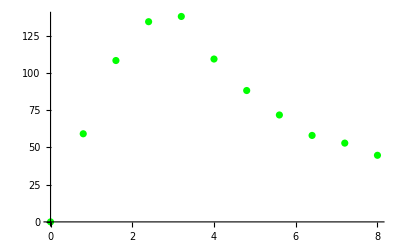

```mathematica
PlotTetra=ListPlot[Re[DistanceDataTetra],PlotStyle->Green]
```

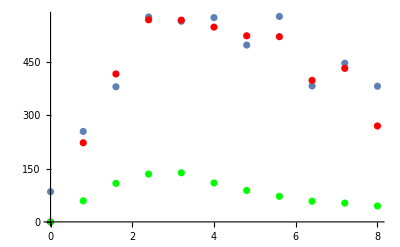

```mathematica
Show[PlotMesMC,PlotBar,PlotTetra]
```